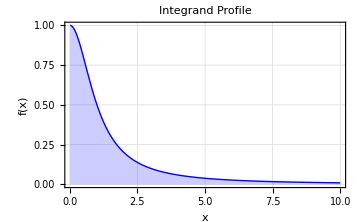
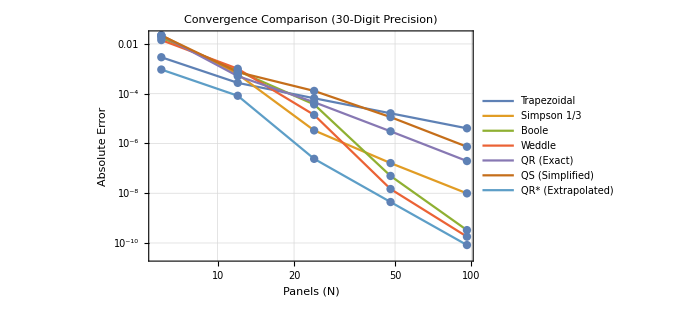
Function: Inverse Tangent Function |    f(x) = 1/(x^2+1) |    Domain: [0.01, 10]
-Graphics-
Equal-Cost Quadrature Results (N = 12 panels / 25 nodes)
Method | Computed Value | Absolute Error | Relative Error
Exact Reference Integral (30-digit) | 1.4611280076170693534 | 0 | 0
QR Exact Rule (Single Panel, 3 nodes) | 1.931411554444035 | 4.703×10^-1 | 3.219×10^-1
QS Simplified Rule (Single Panel, 3 nodes) | 1.963079910196521 | 5.02×10^-1 | 3.435×10^-1
Composite Trapezoidal (2n=24 subintervals) | 1.461401048935962 | 2.73×10^-4 | 1.869×10^-4
Composite Simpson 1/3 (2n=24 subintervals) | 1.460517219331448 | 6.108×10^-4 | 4.18×10^-4
Composite Simpson 3/8 (2n=24 subintervals) | 1.458496569834687 | 2.631×10^-3 | 1.801×10^-3
Composite Boole's Rule (2n=24 subintervals) | 1.461953422887912 | 8.254×10^-4 | 5.649×10^-4
Composite Weddle's Rule (2n=24 subintervals) | 1.462133738928856 | 1.006×10^-3 | 6.883×10^-4
Composite QR Exact (n=12 panels, 25 nodes) | 1.460616642545131 | 5.114×10^-4 | 3.5×10^-4
Composite QS Simplified (n=12 panels, 25 nodes) | 1.46038770180974 | 7.403×10^-4 | 5.067×10^-4
Extrapolated QR* (n=12, 49 nodes) | 1.461210809861016 | 8.28×10^-5 | 5.667×10^-5
Convergence Plot & Observed Orders
-Graphics-
Method | Observed Order of Convergence (p)
Composite Trapezoidal | 2.304
Composite Simpson 1/3 | 5.407
Composite Simpson 3/8 | 5.362
Composite Boole's Rule | 6.543
Composite Weddle's Rule | 6.855
Composite QR Exact | 4.095
Composite QS Simplified | 3.573
Extrapolated QR* | 6.105

```mathematica
(* =========================================================================Circular-Segment Quadrature Rules (QR,QS,and Extrapolated QR) (Reference Implementation in Wolfram Mathematica (30-Digit Precision))
Paper:Circular-segment quadrature rules based on the three-point circumcircle
Authors:Md.Abdur Rahman,Md.Sindid Safwanur Kouly,Dr.Mostak Ahmed
   =========================================================================*)

ClearAll["Global`*"];

(*Precomputed Maclaurin coefficients phi_k for small-t evaluation (Eq.10)*)
phiCoeffs=Table[1/(4^k*(2*k+1))*Binomial[2*k,k]-(-1)^k*Binomial[1/2,k],{k,1,14}];

(* =====================1. Single-Panel QR& QS Rules=====================*)

(*Lemma 1:Graph-validity criterion D^2≤2*(h^2+d_min^2)*)
CheckGraphValidity[f_,a_,b_]:=Module[{aa,bb,h,m,y0,y1,y2,d,sigmaD,dmin},aa=N[a,30];bb=N[b,30];
h=(bb-aa)/2;m=(aa+bb)/2;
y0=N[f[aa],30];y1=N[f[m],30];y2=N[f[bb],30];
d=y0-2*y1+y2;
If[d==0,Return[True]];
sigmaD=Sign[d];
dmin=Min[sigmaD*(y0-y1),sigmaD*(y2-y1)];
d^2≤2*(h^2+dmin^2)];

(*Exact Circular-Segment Rule:QRExact (QR)-Algorithm 1*)
QRExact[f_,a_,b_]:=Module[{aa,bb,h,m,y0,y1,y2,Dval,T,l1,l2,c2,t,theta,R,S},aa=N[a,30];bb=N[b,30];
h=(bb-aa)/2;m=(aa+bb)/2;
y0=N[f[aa],30];y1=N[f[m],30];y2=N[f[bb],30];
Dval=y0-2*y1+y2;
T=h*(y0+y2);
(*Exact collinear fallback*)If[Dval==0,Return[T]];
l1=Sqrt[h^2+(y1-y0)^2];
l2=Sqrt[h^2+(y2-y1)^2];
c2=4*h^2+(y2-y0)^2;
t=Min[1,(h*Abs[Dval])/(l1*l2)];
(*Series evaluation for t<1/4 to avoid subtractive cancellation (Sec.2.5)*)If[t<1/4,S=(c2/4)*Sum[phiCoeffs[[k]]*t^(2*k-1),{k,1,14}],theta=2*ArcSin[t];
R=Sqrt[c2]/(2*t);
S=(R^2/2)*(theta-Sin[theta])];
N[T-Sign[Dval]*S,30]];

(*Simplified Algebraic Rule:QRSimplified (QS)-Eq.(8)*)
QRSimplified[f_,a_,b_]:=Module[{aa,bb,h,m,y0,y1,y2,l1,l2,c2,mu},aa=N[a,30];bb=N[b,30];
h=(bb-aa)/2;m=(aa+bb)/2;
y0=N[f[aa],30];y1=N[f[m],30];y2=N[f[bb],30];
l1=Sqrt[h^2+(y1-y0)^2];
l2=Sqrt[h^2+(y2-y1)^2];
c2=4*h^2+(y2-y0)^2;
mu=c2/(l1*l2);
N[(h/6)*((6-mu)*y0+2*mu*y1+(6-mu)*y2),30]];

(* =====================2. Elementary Newton-Cotes Rules=====================*)

Simpson38Rule[f_,a_,b_]:=Module[{aa,bb,h,y0,y1,y2,y3},aa=N[a,30];bb=N[b,30];h=(bb-aa)/3;
y0=N[f[aa],30];y1=N[f[aa+h],30];
y2=N[f[aa+2*h],30];y3=N[f[bb],30];
N[(3*h/8)*(y0+3*y1+3*y2+y3),30]];

BooleRule[f_,a_,b_]:=Module[{aa,bb,h,y0,y1,y2,y3,y4},aa=N[a,30];bb=N[b,30];h=(bb-aa)/4;
y0=N[f[aa],30];y1=N[f[aa+h],30];y2=N[f[aa+2*h],30];
y3=N[f[aa+3*h],30];y4=N[f[bb],30];
N[(2*h/45)*(7*y0+32*y1+12*y2+32*y3+7*y4),30]];

WeddleRule[f_,a_,b_]:=Module[{aa,bb,h,y0,y1,y2,y3,y4,y5,y6},aa=N[a,30];bb=N[b,30];h=(bb-aa)/6;
y0=N[f[aa],30];y1=N[f[aa+h],30];y2=N[f[aa+2*h],30];
y3=N[f[aa+3*h],30];y4=N[f[aa+4*h],30];y5=N[f[aa+5*h],30];
y6=N[f[bb],30];
N[(3*h/10)*(y0+5*y1+y2+6*y3+y4+5*y5+y6),30]];

(* ============3. Equal-Cost Composite Rules (2*n+1 Nodes)============*)

QRComposite[f_,a_,b_,n_]:=Module[{aa,bb,hSub},aa=N[a,30];bb=N[b,30];hSub=(bb-aa)/n;
N[Sum[QRExact[f,aa+(i-1)*hSub,aa+i*hSub],{i,1,n}],30]];

QSComposite[f_,a_,b_,n_]:=Module[{aa,bb,hSub},aa=N[a,30];bb=N[b,30];hSub=(bb-aa)/n;
N[Sum[QRSimplified[f,aa+(i-1)*hSub,aa+i*hSub],{i,1,n}],30]];

(*Order-6 Richardson Extrapolated Rule:QR*(Section 5.4,uses 4*n+1 nodes)*)
QRExtrapolated[f_,a_,b_,n_]:=Module[{qN,q2N},qN=QRComposite[f,a,b,n];
q2N=QRComposite[f,a,b,2*n];
N[(16*q2N-qN)/15,30]];

TrapezoidalComposite[f_,a_,b_,nPanels_]:=Module[{aa,bb,mSub,h,xList,yList},aa=N[a,30];bb=N[b,30];mSub=2*nPanels;h=(bb-aa)/mSub;
xList=Table[aa+i*h,{i,0,mSub}];
yList=N[f/@xList,30];
N[(h/2)*(yList[[1]]+2*Sum[yList[[i]],{i,2,mSub}]+yList[[mSub+1]]),30]];

Simpson13Composite[f_,a_,b_,nPanels_]:=Module[{aa,bb,mSub,h,xList,yList},aa=N[a,30];bb=N[b,30];mSub=2*nPanels;h=(bb-aa)/mSub;
xList=Table[aa+i*h,{i,0,mSub}];
yList=N[f/@xList,30];
N[(h/3)*(yList[[1]]+4*Sum[yList[[2*i]],{i,1,mSub/2}]+2*Sum[yList[[2*i+1]],{i,1,mSub/2-1}]+yList[[mSub+1]]),30]];

Simpson38Composite[f_,a_,b_,nPanels_]:=Module[{aa,bb,mSub,k,hSub},aa=N[a,30];bb=N[b,30];mSub=2*nPanels;
If[Mod[mSub,3]≠0,Return["Requires 2*nPanels divisible by 3"]];
k=mSub/3;hSub=(bb-aa)/k;
N[Sum[Simpson38Rule[f,aa+(i-1)*hSub,aa+i*hSub],{i,1,k}],30]];

BooleComposite[f_,a_,b_,nPanels_]:=Module[{aa,bb,mSub,k,hSub},aa=N[a,30];bb=N[b,30];mSub=2*nPanels;
If[Mod[mSub,4]≠0,Return["Requires 2*nPanels divisible by 4"]];
k=mSub/4;hSub=(bb-aa)/k;
N[Sum[BooleRule[f,aa+(i-1)*hSub,aa+i*hSub],{i,1,k}],30]];

WeddleComposite[f_,a_,b_,nPanels_]:=Module[{aa,bb,mSub,k,hSub},aa=N[a,30];bb=N[b,30];mSub=2*nPanels;
If[Mod[mSub,6]≠0,Return["Requires 2*nPanels divisible by 6"]];
k=mSub/6;hSub=(bb-aa)/k;
N[Sum[WeddleRule[f,aa+(i-1)*hSub,aa+i*hSub],{i,1,k}],30]];

(* =====================4. Single-Function Analyzer=====================*)

AnalyzeSingleFunction[name_,fExpr_,a_,b_,nPanels_]:=Module[{f,exact,methodNames,methodValues,methodErrors,resultsTable,minError,highlightRowIdx,styledTable,nValues,hValues,errTrap,errSimp13,errSimp38,errBoole,errWeddle,errQR,errQS,errQRStar,calcSlope,orderTable,plotObj,functionPlot},f=(fExpr/.x->#)&;
exact=Quiet[NIntegrate[f[t],{t,a,b},WorkingPrecision->30]];
methodNames={"QR Exact Rule (Single Panel, 3 nodes)","QS Simplified Rule (Single Panel, 3 nodes)",Row[{"Composite Trapezoidal (2n=",2*nPanels," subintervals)"}],Row[{"Composite Simpson 1/3 (2n=",2*nPanels," subintervals)"}],Row[{"Composite Simpson 3/8 (2n=",2*nPanels," subintervals)"}],Row[{"Composite Boole's Rule (2n=",2*nPanels," subintervals)"}],Row[{"Composite Weddle's Rule (2n=",2*nPanels," subintervals)"}],Row[{"Composite QR Exact (n=",nPanels," panels, ",2*nPanels+1," nodes)"}],Row[{"Composite QS Simplified (n=",nPanels," panels, ",2*nPanels+1," nodes)"}],Row[{"Extrapolated QR* (n=",nPanels,", ",4*nPanels+1," nodes)"}]};
methodValues={QRExact[f,a,b],QRSimplified[f,a,b],TrapezoidalComposite[f,a,b,nPanels],Simpson13Composite[f,a,b,nPanels],Simpson38Composite[f,a,b,nPanels],BooleComposite[f,a,b,nPanels],WeddleComposite[f,a,b,nPanels],QRComposite[f,a,b,nPanels],QSComposite[f,a,b,nPanels],QRExtrapolated[f,a,b,nPanels]};
methodErrors=Abs[exact-methodValues];
resultsTable=Prepend[Table[{methodNames[[i]],NumberForm[N[methodValues[[i]],30],20],ScientificForm[N[methodErrors[[i]],6],4],ScientificForm[N[If[Abs[exact]>0,methodErrors[[i]]/Abs[exact],0],6],4]},{i,Length[methodValues]}],{"Method","Computed Value","Absolute Error","Relative Error"}];
resultsTable=Insert[resultsTable,{"Exact Reference Integral (30-digit)",NumberForm[N[exact,30],20],"0","0"},2];
minError=Min[methodErrors];
highlightRowIdx=First[Position[methodErrors,minError]][[1]]+2;
styledTable=MapIndexed[If[First[#2]==highlightRowIdx,Map[Item[#,Background->LightGreen]&,#1],#1]&,resultsTable];
nValues={6,12,24,48,96};
hValues=(b-a)/nValues;
errTrap=Table[Abs[exact-TrapezoidalComposite[f,a,b,nv]],{nv,nValues}];
errSimp13=Table[Abs[exact-Simpson13Composite[f,a,b,nv]],{nv,nValues}];
errSimp38=Table[Abs[exact-Simpson38Composite[f,a,b,nv]],{nv,nValues}];
errBoole=Table[Abs[exact-BooleComposite[f,a,b,nv]],{nv,nValues}];
errWeddle=Table[Abs[exact-WeddleComposite[f,a,b,nv]],{nv,nValues}];
errQR=Table[Abs[exact-QRComposite[f,a,b,nv]],{nv,nValues}];
errQS=Table[Abs[exact-QSComposite[f,a,b,nv]],{nv,nValues}];
errQRStar=Table[Abs[exact-QRExtrapolated[f,a,b,nv]],{nv,nValues}];
calcSlope[errList_]:=Module[{validData,logH,logE,fit},validData=Select[Transpose[{hValues,errList}],#[[2]]>10^-25&];
If[Length[validData]<2,Return[0.0]];
logH=Log[validData[[All,1]]];
logE=Log[validData[[All,2]]];
fit=Fit[Transpose[{logH,logE}],{1,x},x];
Coefficient[fit,x,1]];
orderTable=Grid[{{"Method","Observed Order of Convergence (p)"},{"Composite Trapezoidal",NumberForm[calcSlope[errTrap],{4,3}]},{"Composite Simpson 1/3",NumberForm[calcSlope[errSimp13],{4,3}]},{"Composite Simpson 3/8",NumberForm[calcSlope[errSimp38],{4,3}]},{"Composite Boole's Rule",NumberForm[calcSlope[errBoole],{4,3}]},{"Composite Weddle's Rule",NumberForm[calcSlope[errWeddle],{4,3}]},{"Composite QR Exact",NumberForm[calcSlope[errQR],{4,3}]},{"Composite QS Simplified",NumberForm[calcSlope[errQS],{4,3}]},{"Extrapolated QR*",NumberForm[calcSlope[errQRStar],{4,3}]}},Frame->All,Alignment->Left,Spacings->{2,1},Background->{None,{LightBlue,None}}];
plotObj=ListLogLogPlot[{Transpose[{nValues,errTrap}],Transpose[{nValues,errSimp13}],Transpose[{nValues,errBoole}],Transpose[{nValues,errWeddle}],Transpose[{nValues,errQR}],Transpose[{nValues,errQS}],Transpose[{nValues,errQRStar}]},Joined->True,Mesh->All,PlotLegends->{"Trapezoidal","Simpson 1/3","Boole","Weddle","QR (Exact)","QS (Simplified)","QR* (Extrapolated)"},GridLines->Automatic,Frame->True,FrameLabel->{"Panels (N)","Absolute Error"},PlotLabel->Style["Convergence Comparison (30-Digit Precision)",12,Bold],ImageSize->500];
functionPlot=Plot[f[x],{x,a,b},PlotRange->All,PlotStyle->{Blue,Thick},Filling->Axis,Frame->True,FrameLabel->{"x","f(x)"},PlotLabel->Style["Integrand Profile",14,Bold],GridLines->Automatic,ImageSize->Medium];
Column[{Grid[{{Style[Row[{"Function: ",name}],15,Bold],Style[Row[{"   f(x) = ",TraditionalForm[fExpr]}],15,Bold,Darker[Blue]],Style[Row[{"   Domain: [",a,", ",b,"]"}],14,Bold]}}],functionPlot,Style[Row[{"Equal-Cost Quadrature Results (N = ",nPanels," panels / ",2*nPanels+1," nodes)"}],12,Bold],Grid[styledTable,Frame->All,Alignment->Left,Spacings->{2,1},Background->{None,{LightBlue,None}}],Style["Convergence Plot & Observed Orders",12,Bold],plotObj,orderTable}]];

(* =====================5. Example Run=====================*)

Clear[x];
name="Inverse Tangent Function";
fExpr=1/(1+x^2);
a=0.01;
b=10;
nPanels=12;

AnalyzeSingleFunction[name,fExpr,a,b,nPanels]
```